```mathematica
ClearAll["Global`*"]
Sum[ (-1)^(5j/6+1)/j,{j,1,Infinity}]
```

Log[1-(-1)^(5/6)]

```mathematica
cyc := {1,1,1,-7,1,1,1,1}
ee[n_, 0,m_] := 1; ee[n_, k_ , m_]:=ee[n,k,m]= Sum[ cyc[[1+Mod[j-1,Length[cyc]]]]ee[Floor[n/j],k-1,m],{j,2,n}]
e1[n_, z_,m_] := Sum[ Binomial[ z,k] ee[n,k,m],{k,0,Log[2,n]}]
Table[ {n,Limit[ (e1[n,z,a=1/4]-1)/z,z->0]-Limit[ (e1[n-1,z,a]-1)/z,z->0]},{n,2, 30}]//TableForm
```

2 | 1
3 | 1
4 | -15/2
5 | 1
6 | 0
7 | 1
8 | 25/3
9 | 1/2
10 | 0
11 | 1
12 | 0
13 | 1
14 | 0
15 | 0
16 | -127/4
17 | 1
18 | 0
19 | 1
20 | 0
21 | 0
22 | 0
23 | 1
24 | 0
25 | 1/2
26 | 0
27 | 1/3
28 | 0
29 | 1
30 | 0

```mathematica
d1[100,3]
```

22-7 ⅈ

```mathematica
cyc[[2]]
```

-1

```mathematica
Table[cyc[[1+Mod[n-1,Length[cyc]]]],{n,1,20}]
```

{1,-1,-2,2,1,-1,-2,2,1,-1,-2,2,1,-1,-2,2,1,-1,-2,2}

```mathematica
Table[1+Mod[n-1,Length[cyc]],{n,1,20}]
```

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}

```mathematica
p[n_, k_] := p[n,k]=Sum[ 1/k-p[Floor[n/j],k+1],{j,2,n}]
```

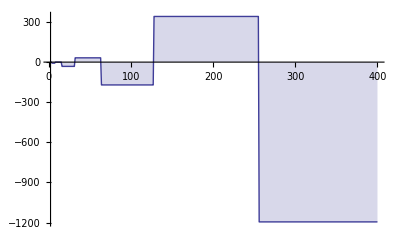

```mathematica
DiscretePlot[ Limit[ (e1[n,z,a=1/4]-1)/z,z->0]-p[n,1],{n,2, 400}]//TableForm
```

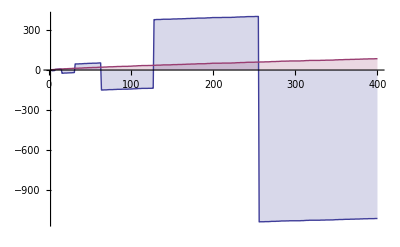

```mathematica
DiscretePlot[ {Limit[ (e1[n,z,a=1/4]-1)/z,z->0],p[n,1]},{n,2, 400}]//TableForm
```

```mathematica
Table[ {n,Limit[ (e1[n,z,a=1/4]-1)/z,z->0]-p[n,1]},{n,2, 100}]//TableForm
```

2 | 0
3 | 0
4 | -8
5 | -8
6 | -8
7 | -8
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | -32
17 | -32
18 | -32
19 | -32
20 | -32
21 | -32
22 | -32
23 | -32
24 | -32
25 | -32
26 | -32
27 | -32
28 | -32
29 | -32
30 | -32
31 | -32
32 | 32
33 | 32
34 | 32
35 | 32
36 | 32
37 | 32
38 | 32
39 | 32
40 | 32
41 | 32
42 | 32
43 | 32
44 | 32
45 | 32
46 | 32
47 | 32
48 | 32
49 | 32
50 | 32
51 | 32
52 | 32
53 | 32
54 | 32
55 | 32
56 | 32
57 | 32
58 | 32
59 | 32
60 | 32
61 | 32
62 | 32
63 | 32
64 | -512/3
65 | -512/3
66 | -512/3
67 | -512/3
68 | -512/3
69 | -512/3
70 | -512/3
71 | -512/3
72 | -512/3
73 | -512/3
74 | -512/3
75 | -512/3
76 | -512/3
77 | -512/3
78 | -512/3
79 | -512/3
80 | -512/3
81 | -512/3
82 | -512/3
83 | -512/3
84 | -512/3
85 | -512/3
86 | -512/3
87 | -512/3
88 | -512/3
89 | -512/3
90 | -512/3
91 | -512/3
92 | -512/3
93 | -512/3
94 | -512/3
95 | -512/3
96 | -512/3
97 | -512/3
98 | -512/3
99 | -512/3
100 | -512/3

```mathematica
d[x_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[x]}];FI[x_]:=FactorInteger[x];FI[1]:={}
Dd[x_,z_]:=Sum[d[j,z],{j,1,x}]
```

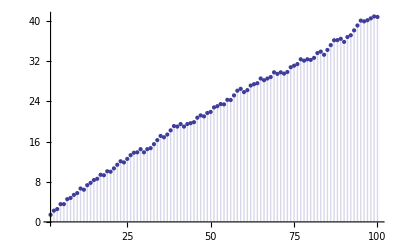

```mathematica
DiscretePlot[ Abs[Dd[n,-I]],{n,2,100}]
```

```mathematica
Dd[100,-I]
```

-2881/72-(65 ⅈ)/8

```mathematica
Sum[ 1/2^j,{j,1,Infinity}]
```

1

```mathematica
Sum[ (-1)^(j+1)/2^j,{j,1,Infinity}]
```

1/3

```mathematica
t [n_, j_] := Mod[n,j]-Mod[n-1,j]
```

```mathematica
Sum[ t[j,3]/2^j,{j,1,Infinity}]
```

4/7

```mathematica
Sum[ t[j,4]/2^j,{j,1,Infinity}]
```

11/15

```mathematica
Sum[ t[j,5]/2^j,{j,1,Infinity}]
```

26/31

```mathematica
Sum[ t[j,2]/3^j,{j,1,Infinity}]
```

1/4

```mathematica
Sum[ t[j,3]/3^j,{j,1,Infinity}]
```

5/13

```mathematica
Sum[ t[j,3]/4^j,{j,1,Infinity}]
```

2/7

```mathematica
Sum[ t[j,3]/5^j,{j,1,Infinity}]
```

7/31

```mathematica
Sum[ Abs[t[j,3]]/5^j,{j,1,Infinity}]
```

8/31

```mathematica
Sum[ t[j,3]/c^j,{j,1,Infinity}]
```

(2+c)/(1+c+c^2)

```mathematica
Sum[Abs[ t[j,3]]/c^j,{j,1,Infinity}]
```

(2+c+c^2)/(-1+c^3)

```mathematica
Sum[ t[j,4]/c^j,{j,1,Infinity}]
```

(3+2 c+c^2)/(1+c+c^2+c^3)

```mathematica
Sum[Abs[ t[j,4]]/c^j,{j,1,Infinity}]
```

(3+c+c^2+c^3)/(-1+c^4)

```mathematica
Sum[ t[j,5]/c^j,{j,1,Infinity}]
```

(4+3 c+2 c^2+c^3)/(1+c+c^2+c^3+c^4)

```mathematica
Sum[Abs[ t[j,5]]/c^j,{j,1,Infinity}]
```

(4+c+c^2+c^3+c^4)/(-1+c^5)

```mathematica
dAlt[x_,z_]:=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[x]}];FI[x_]:=FactorInteger[x];FI[1]:={}
```

```mathematica
D[dAlt[x,z],z]/.z->0
```

FactorInteger::exact: Argument x in FactorInteger[x] is not an exact number.

Part::partd: Part specification p ⟦ 2 ⟧ is longer than depth of object.

FactorInteger::exact: Argument x in FactorInteger[x] is not an exact number.

Part::partd: Part specification p ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

General::ivar: 0 is not a valid variable.

∂_0 ∏_p^FactorInteger[x] (-1)^p⟦2⟧ Binomial[0,p⟦2⟧]

```mathematica
x^(1/2) Sum[ (-1)^(n-1)(Log[x])^n/(n! 2^(n-1))Sum[ 1/(2 k + 1 ),{k,0,(n-1)/2}], {n,1,Infinity}]
```

√x ∑_(n=1)^∞ ((-1)^(-1+n) 2^-n Log[x]^n (-PolyGamma[0,1/2]+PolyGamma[0,1+n/2]))/(n!)

```mathematica
vv[x_] := x^(1/2) Sum[ (-1)^(n-1)(Log[x])^n/((n!) 2^(n-1))Sum[ 1/(2 k + 1 ),{k,0,Floor[(n-1)/2]}], {n,1,Infinity}]
```

```mathematica
N[vv[100.]]
```

$Aborted

```mathematica
LogIntegral[100.] - Log[Log[100.]]-EulerGamma
```

28.0217

```mathematica
LL[ x_, 1, a_] := LL[x,1,a]=Sum[ Log[ (j+a)/(a-1)], {j,0,Floor[ x-a]}]
LL[ x_, k_, a_ ] := LL[x,k,a]=Sum[ LL[x/(j+a), k-1, a], {j,0,Floor[x-a]}]
LC[x_, k_, a_ ] := a^(-k) LL[ x a^k, k, a+1]
L1[x_, z_, a_ ] := Sum[ Binomial[ z,k] LC[x,k,a],{k,1, Log[2,2a x]}]
```

```mathematica
N[L1[100,-1,1]]
```

-94.0453

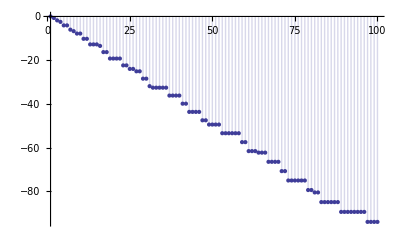

```mathematica
DiscretePlot[ L1[n,-1,1],{n,1,100}]
```